```mathematica
SetOptions[InputNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},TrackCellChangeTimes->False]
```

```mathematica
raw$afs=Import["/Users/andy/Code/data/motion/cmu/sport/06.asf", "String"];
raw$amc=Import["/Users/andy/Code/data/motion/cmu/sport/06_15.amc", "String"];
```

```mathematica
ParseAFS[raw_]:=Block[
{
str=raw,
blocks,

bones,
hierarchy,
$
},

(*drop comments*)
str=StringTrim@StringReplacePart[
str,
"",
StringPosition[str,Shortest[StringExpression["#"~~___~~EndOfLine]]]
];

blocks=
Association[
#[[1]]->#[[2;;]]&/@Map[
StringTrim/@StringSplit[#,"\n"]&,
StringSplit[str,":"]
]
];

bones=Block[
{
splits=Map[
Association[#[[1]]->#[[2;;]]&/@StringSplit[#]]&,
blocks["bonedata"][[#[[1]]+1;;#[[2]]-1]]&/@Transpose[{
Flatten[Position[blocks["bonedata"],"begin"]],
Flatten[Position[blocks["bonedata"],"end"]]
}]
]
},

Association@Map[
#["name"]->#&,
Map[
Block[
{
id=#["id"][[1]],
name=#["name"][[1]],
direction=Internal`StringToDouble/@#["direction"],
length=#["length"][[1]],
axis={Internal`StringToDouble[#]Degree&/@#["axis"][[1;;3]],#["axis"][[4]]},
dof=If[
KeyExistsQ[#,"dof"],
Flatten[{
If[MemberQ[#["dof"],"rx"],Position[#["dof"],"rx"],-1],
If[MemberQ[#["dof"],"ry"],Position[#["dof"],"ry"],-1],
If[MemberQ[#["dof"],"rz"],Position[#["dof"],"rz"],-1]
}],
{-1, -1, -1}
]
},
<|
"id"-> id,
"name"->name,
"direction"-> direction,
"length"->Internal`StringToDouble[length],
"axis"-> axis,
"dof"->dof
|>
]&,
splits
]
]

];


hierarchy=
Block[
{
paths=StringSplit/@blocks["hierarchy"][[2;;-2]],
v,
e
},
v=Flatten[paths]//DeleteDuplicates;
e=Flatten@Map[
Block[
{
parent=#[[1]], 
children=#[[2;;]]
},
parent->#&/@children
]&,
paths
];


Association@SortBy[
Map[
#->Reverse@FindShortestPath[
Graph[e],
"root",
#
]&,
v
],
Length[#[[2]]]&
]
];

$=Association@Map[
Block[
{
bone=#,

axis,
C,
Cinv,

parent,
B,

offset
},

(*First create a matrix C from the axis using the axis order to determine the order the rotation values are composed.*)
axis=bones[bone]["axis"];
C=TransformationMatrix[
Composition[
RotationTransform[axis[[1,1]],{1,0,0}],
RotationTransform[axis[[1,2]],{0,1,0}],
RotationTransform[axis[[1,3]],{0,0,1}]
]
];
(*C=Dot[
RotationTransform[axis[[1,3]],{0,0,1}]//TransformationMatrix,
RotationTransform[axis[[1,2]],{0,1,0}]//TransformationMatrix,
RotationTransform[axis[[1,1]],{1,0,0}]//TransformationMatrix
];*)

Cinv=Inverse[C];

(*reate a matrix B and from the translation offset from the segments parent.The translation offset is the direction and length of the parent segment.*)
parent=hierarchy[bone][[2]];

B=If[
parent≠"root",
TransformationMatrix[
TranslationTransform[
bones[parent]["direction"]*bones[parent]["length"]
]
],
IdentityMatrix[4]
];

(*;;-2=exclude root*)
offset=Total[bones[#]["direction"]*bones[#]["length"]&/@hierarchy[bone][[;;-2]]];

bone-><|"C"->C,"Cinv"->Cinv,"B"->B,"offset"->offset|>
]&,
Keys[bones]
];

{hierarchy,bones,$}
];
```

```mathematica
ParseAMC[raw_]:=Block[
{
str=raw,
blocks,
frames
},

(*drop comments*)
str=StringTrim@StringReplacePart[
str,
"",
StringPosition[str,Shortest[StringExpression[("#"|":")~~___~~EndOfLine]],Overlaps->False]
];

blocks=StringTrim/@StringSplit[str,"\n"];

frames=
Map[
Block[
{
data=blocks[[#[[1]];;#[[2]]-1]],

index,
values
},
index=data[[1]];
values={#[[1]],Internal`StringToDouble/@#[[2;;]]}&/@(StringSplit[#,Whitespace]&/@data[[2;;]]);
{index,values}
]&,
Partition[
Riffle[
Flatten[Position[blocks,_String?DigitQ]],
Flatten[Position[blocks,_String?DigitQ]][[2;;]]
],
2
]
];

frames
];
```

```mathematica
{hierarchy,bones,$}=ParseAFS[raw$afs];
```

```mathematica
motion=ParseAMC[raw$amc];
```

```mathematica
out=Table[
Block[
{
frame=motion[[i]],

transforms,
locals,
v
},
transforms=frame[[2]];

locals=Association@Map[
Block[
{
bone=#[[1]],
transform=#[[2]],

L
},

If[
bone=="root",
L=
TransformationMatrix[
Composition[
TranslationTransform[transform[[1;;3]]],
RotationTransform[transform[[6]]Degree,{0,0,1}],
RotationTransform[transform[[5]]Degree,{0,1,0}],
RotationTransform[transform[[4]]Degree,{1,0,0}]


]
],

(*else*)
L=Block[
{
dof=If[KeyExistsQ[bones[bone],"dof"],bones[bone]["dof"],{-1,-1,-1}],
rx,ry,rz,
trx,try,trz,
Cinv,M,C,B
},

rx=If[dof[[1]]≠-1,transform[[dof[[1]]]]Degree,-1];
ry=If[dof[[2]]≠-1,transform[[dof[[2]]]]Degree,-1];
rz=If[dof[[3]]≠-1,transform[[dof[[3]]]]Degree,-1];

Cinv=$[bone]["Cinv"];
C=$[bone]["C"];
B=$[bone]["B"];

trx=If[
rx≠-1,
RotationTransform[rx,{1,0,0}],
TransformationFunction[IdentityMatrix[4]]
];

try=If[
ry≠-1,
RotationTransform[ry,{0,1,0}],
TransformationFunction[IdentityMatrix[4]]
];

trz=If[
rz≠-1,
RotationTransform[rz,{0,0,1}],
TransformationFunction[IdentityMatrix[4]]
];

M=Dot[


trx//TransformationMatrix,
try//TransformationMatrix,
trz//TransformationMatrix

];
M=TransformationMatrix[
Composition[
trx,
try,
trz
]
];

Dot[Cinv,M,C,B]
]
];
bone->L

]&,
transforms
];


v=Association@Map[
Block[
{
bone=#[[1]],
path=#[[2]],

global=IdentityMatrix[4],
offset
},

offset=
If[
KeyExistsQ[$,bone],
$[bone]["offset"],
{0,0,0}
];

Map[
If[
KeyExistsQ[locals,#],
global=Dot[global,locals[#]]
]&,
path//Reverse
];

bone->offset+(global[[1;;3,-1]])

]&,
Normal[hierarchy]
];

v
],

{i,1,Length[motion],10}
];
```

```mathematica
out//Length
```

55

```mathematica
plotrange={Min[#],Max[#]}&/@Transpose[Flatten[Normal[out],1][[All,2]]];

ListAnimate[
Map[
Graphics3D[
Block[
{v=#},
{
InfinitePlane[{{1,plotrange[[2,1]],0},{1,plotrange[[2,1]],1},{0,plotrange[[2,1]],1}}],
Sphere[v["head"]],

Map[
Line[v[#]&/@hierarchy[#]]&,
Keys[hierarchy]
]
}
],
Boxed->False,
PlotRange->plotrange,
SphericalRegion->True,
ViewPoint->{0,2,-2}
]&,
out[[;;;;1]]
],
15
]
```

```mathematica
hierarchy
```

<|root→{root},lhipjoint→{lhipjoint,root},lowerback→{lowerback,root},rhipjoint→{rhipjoint,root},lfemur→{lfemur,lhipjoint,root},rfemur→{rfemur,rhipjoint,root},upperback→{upperback,lowerback,root},ltibia→{ltibia,lfemur,lhipjoint,root},rtibia→{rtibia,rfemur,rhipjoint,root},thorax→{thorax,upperback,lowerback,root},lclavicle→{lclavicle,thorax,upperback,lowerback,root},lfoot→{lfoot,ltibia,lfemur,lhipjoint,root},lowerneck→{lowerneck,thorax,upperback,lowerback,root},rclavicle→{rclavicle,thorax,upperback,lowerback,root},rfoot→{rfoot,rtibia,rfemur,rhipjoint,root},lhumerus→{lhumerus,lclavicle,thorax,upperback,lowerback,root},ltoes→{ltoes,lfoot,ltibia,lfemur,lhipjoint,root},rhumerus→{rhumerus,rclavicle,thorax,upperback,lowerback,root},rtoes→{rtoes,rfoot,rtibia,rfemur,rhipjoint,root},upperneck→{upperneck,lowerneck,thorax,upperback,lowerback,root},head→{head,upperneck,lowerneck,thorax,upperback,lowerback,root},lradius→{lradius,lhumerus,lclavicle,thorax,upperback,lowerback,root},rradius→{rradius,rhumerus,rclavicle,thorax,upperback,lowerback,root},lwrist→{lwrist,lradius,lhumerus,lclavicle,thorax,upperback,lowerback,root},rwrist→{rwrist,rradius,rhumerus,rclavicle,thorax,upperback,lowerback,root},lhand→{lhand,lwrist,lradius,lhumerus,lclavicle,thorax,upperback,lowerback,root},lthumb→{lthumb,lwrist,lradius,lhumerus,lclavicle,thorax,upperback,lowerback,root},rhand→{rhand,rwrist,rradius,rhumerus,rclavicle,thorax,upperback,lowerback,root},rthumb→{rthumb,rwrist,rradius,rhumerus,rclavicle,thorax,upperback,lowerback,root},lfingers→{lfingers,lhand,lwrist,lradius,lhumerus,lclavicle,thorax,upperback,lowerback,root},rfingers→{rfingers,rhand,rwrist,rradius,rhumerus,rclavicle,thorax,upperback,lowerback,root}|>

```mathematica
Block[
{
frames=Sort[Normal[#]]&/@out,

index,
data,
out
},

If[
Not[Equal[frames[[All,All,1]]]],
Abort[]
];

index=frames[[1,All,1]];
data=Flatten[#[[All,2]]]&/@frames;

out={
"meta"->{
"markers"->index,
"hierarchy"->hierarchy
},
"data"->data[[1;;1]]
};

Export[
"/Users/andy/Code/data/motion/cmu/dance/94_01_signle.json",
out,
"Compact"->True
]
]
```

/Users/andy/Code/data/motion/cmu/dance/94_01_signle.json

```mathematica
out
```

{<|root→{-30.184,12.9578,14.9131},lhipjoint→{-28.9003,11.3731,15.7885},lowerback→{-30.1722,14.7221,14.8492},25,rthumb→{-43.0273,19.8884,8.66118},lfingers→{-13.0282,21.0197,8.51525},rfingers→{-43.1352,19.9129,7.72988}|>,359,<|root→{1},29,1|>}
 |  |  |  |

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

```mathematica
g=Graph[
DeleteDuplicates@Flatten@Map[
Block[
{
from=#[[1]],
to=#[[2]]
},
#[[2]]-> #[[1]]&/@Partition[Riffle[to[[1;;]],to[[2;;]]],2]
]&,
Select[Normal[hierarchy],Length[#[[2]]]>1&]
],

VertexShapeFunction->"Name"
];

c=VertexList[g]
```

{root,lhipjoint,lowerback,rhipjoint,lfemur,rfemur,upperback,ltibia,rtibia,thorax,lclavicle,lfoot,lowerneck,rclavicle,rfoot,lhumerus,ltoes,rhumerus,rtoes,upperneck,head,lradius,rradius,lwrist,rwrist,lhand,lthumb,rhand,rthumb,lfingers,rfingers}

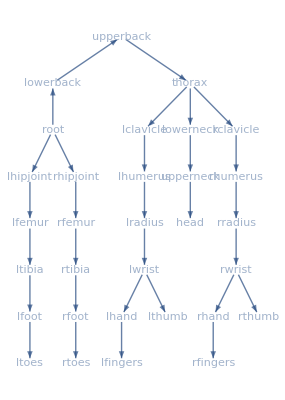

```mathematica
g
```

```mathematica
Sort@MapIndexed[
{
"id"->Position[Sort[c],c[[#2[[1]]]]][[1,1]]-1,
"at"->Position[Sort[c],c[[#2[[1]]]]][[1,1]]-1,
"name"->c[[#2[[1]]]],
"e"->(Position[Sort[c],#][[1,1]]-1&/@c[[Flatten@Position[#,1]]])
}&,
Normal[AdjacencyMatrix[g]]
];
ExportString[
%,
"JSON"
]
```

[
    {
        "id": 0,
        "at": 0,
        "name": "head",
        "e": []
    },
    {
        "id": 1,
        "at": 1,
        "name": "lclavicle",
        "e": [
            7
        ]
    },
    {
        "id": 2,
        "at": 2,
        "name": "lfemur",
        "e": [
            12
        ]
    },
    {
        "id": 3,
        "at": 3,
        "name": "lfingers",
        "e": []
    },
    {
        "id": 4,
        "at": 4,
        "name": "lfoot",
        "e": [
            13
        ]
    },
    {
        "id": 5,
        "at": 5,
        "name": "lhand",
        "e": [
            3
        ]
    },
    {
        "id": 6,
        "at": 6,
        "name": "lhipjoint",
        "e": [
            2
        ]
    },
    {
        "id": 7,
        "at": 7,
        "name": "lhumerus",
        "e": [
            10
        ]
    },
    {
        "id": 8,
        "at": 8,
        "name": "lowerback",
        "e": [
            29
        ]
    },
    {
        "id": 9,
        "at": 9,
        "name": "lowerneck",
        "e": [
            30
        ]
    },
    {
        "id": 10,
        "at": 10,
        "name": "lradius",
        "e": [
            14
        ]
    },
    {
        "id": 11,
        "at": 11,
        "name": "lthumb",
        "e": []
    },
    {
        "id": 12,
        "at": 12,
        "name": "ltibia",
        "e": [
            4
        ]
    },
    {
        "id": 13,
        "at": 13,
        "name": "ltoes",
        "e": []
    },
    {
        "id": 14,
        "at": 14,
        "name": "lwrist",
        "e": [
            5,
            11
        ]
    },
    {
        "id": 15,
        "at": 15,
        "name": "rclavicle",
        "e": [
            21
        ]
    },
    {
        "id": 16,
        "at": 16,
        "name": "rfemur",
        "e": [
            25
        ]
    },
    {
        "id": 17,
        "at": 17,
        "name": "rfingers",
        "e": []
    },
    {
        "id": 18,
        "at": 18,
        "name": "rfoot",
        "e": [
            26
        ]
    },
    {
        "id": 19,
        "at": 19,
        "name": "rhand",
        "e": [
            17
        ]
    },
    {
        "id": 20,
        "at": 20,
        "name": "rhipjoint",
        "e": [
            16
        ]
    },
    {
        "id": 21,
        "at": 21,
        "name": "rhumerus",
        "e": [
            23
        ]
    },
    {
        "id": 22,
        "at": 22,
        "name": "root",
        "e": [
            6,
            8,
            20
        ]
    },
    {
        "id": 23,
        "at": 23,
        "name": "rradius",
        "e": [
            27
        ]
    },
    {
        "id": 24,
        "at": 24,
        "name": "rthumb",
        "e": []
    },
    {
        "id": 25,
        "at": 25,
        "name": "rtibia",
        "e": [
            18
        ]
    },
    {
        "id": 26,
        "at": 26,
        "name": "rtoes",
        "e": []
    },
    {
        "id": 27,
        "at": 27,
        "name": "rwrist",
        "e": [
            19,
            24
        ]
    },
    {
        "id": 28,
        "at": 28,
        "name": "thorax",
        "e": [
            1,
            9,
            15
        ]
    },
    {
        "id": 29,
        "at": 29,
        "name": "upperback",
        "e": [
            28
        ]
    },
    {
        "id": 30,
        "at": 30,
        "name": "upperneck",
        "e": [
            0
        ]
    }
]

```mathematica
ExportString[
Sort@MapIndexed[
c[[#2[[1]]]]->c[[Flatten@Position[#,1]]]&,
Normal[AdjacencyMatrix[g]]
],
"JSON"
]
```

{
    "head": [
        "upperneck"
    ],
    "lclavicle": [
        "thorax",
        "lhumerus"
    ],
    "lfemur": [
        "lhipjoint",
        "ltibia"
    ],
    "lfingers": [
        "lhand"
    ],
    "lfoot": [
        "ltibia",
        "ltoes"
    ],
    "lhand": [
        "lwrist",
        "lfingers"
    ],
    "lhipjoint": [
        "root",
        "lfemur"
    ],
    "lhumerus": [
        "lclavicle",
        "lradius"
    ],
    "lowerback": [
        "root",
        "upperback"
    ],
    "lowerneck": [
        "thorax",
        "upperneck"
    ],
    "lradius": [
        "lhumerus",
        "lwrist"
    ],
    "lthumb": [
        "lwrist"
    ],
    "ltibia": [
        "lfemur",
        "lfoot"
    ],
    "ltoes": [
        "lfoot"
    ],
    "lwrist": [
        "lradius",
        "lhand",
        "lthumb"
    ],
    "rclavicle": [
        "thorax",
        "rhumerus"
    ],
    "rfemur": [
        "rhipjoint",
        "rtibia"
    ],
    "rfingers": [
        "rhand"
    ],
    "rfoot": [
        "rtibia",
        "rtoes"
    ],
    "rhand": [
        "rwrist",
        "rfingers"
    ],
    "rhipjoint": [
        "root",
        "rfemur"
    ],
    "rhumerus": [
        "rclavicle",
        "rradius"
    ],
    "root": [
        "lhipjoint",
        "lowerback",
        "rhipjoint"
    ],
    "rradius": [
        "rhumerus",
        "rwrist"
    ],
    "rthumb": [
        "rwrist"
    ],
    "rtibia": [
        "rfemur",
        "rfoot"
    ],
    "rtoes": [
        "rfoot"
    ],
    "rwrist": [
        "rradius",
        "rhand",
        "rthumb"
    ],
    "thorax": [
        "upperback",
        "lclavicle",
        "lowerneck",
        "rclavicle"
    ],
    "upperback": [
        "lowerback",
        "thorax"
    ],
    "upperneck": [
        "lowerneck",
        "head"
    ]
}

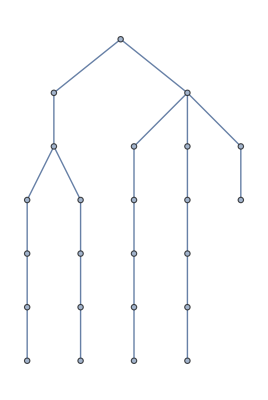

```mathematica
g
```

```mathematica
Normal[hierarchy]
```

{root→{root},lhipjoint→{lhipjoint,root},lowerback→{lowerback,root},rhipjoint→{rhipjoint,root},lfemur→{lfemur,lhipjoint,root},rfemur→{rfemur,rhipjoint,root},upperback→{upperback,lowerback,root},ltibia→{ltibia,lfemur,lhipjoint,root},rtibia→{rtibia,rfemur,rhipjoint,root},thorax→{thorax,upperback,lowerback,root},lclavicle→{lclavicle,thorax,upperback,lowerback,root},lfoot→{lfoot,ltibia,lfemur,lhipjoint,root},lowerneck→{lowerneck,thorax,upperback,lowerback,root},rclavicle→{rclavicle,thorax,upperback,lowerback,root},rfoot→{rfoot,rtibia,rfemur,rhipjoint,root},lhumerus→{lhumerus,lclavicle,thorax,upperback,lowerback,root},ltoes→{ltoes,lfoot,ltibia,lfemur,lhipjoint,root},rhumerus→{rhumerus,rclavicle,thorax,upperback,lowerback,root},rtoes→{rtoes,rfoot,rtibia,rfemur,rhipjoint,root},upperneck→{upperneck,lowerneck,thorax,upperback,lowerback,root},head→{head,upperneck,lowerneck,thorax,upperback,lowerback,root},lradius→{lradius,lhumerus,lclavicle,thorax,upperback,lowerback,root},rradius→{rradius,rhumerus,rclavicle,thorax,upperback,lowerback,root},lwrist→{lwrist,lradius,lhumerus,lclavicle,thorax,upperback,lowerback,root},rwrist→{rwrist,rradius,rhumerus,rclavicle,thorax,upperback,lowerback,root},lhand→{lhand,lwrist,lradius,lhumerus,lclavicle,thorax,upperback,lowerback,root},lthumb→{lthumb,lwrist,lradius,lhumerus,lclavicle,thorax,upperback,lowerback,root},rhand→{rhand,rwrist,rradius,rhumerus,rclavicle,thorax,upperback,lowerback,root},rthumb→{rthumb,rwrist,rradius,rhumerus,rclavicle,thorax,upperback,lowerback,root},lfingers→{lfingers,lhand,lwrist,lradius,lhumerus,lclavicle,thorax,upperback,lowerback,root},rfingers→{rfingers,rhand,rwrist,rradius,rhumerus,rclavicle,thorax,upperback,lowerback,root}}

```mathematica
TableForm[Normal@AdjacencyMatrix[g],TableHeadings->{c=Style[#,Blue]&/@%,c}];
TableForm[Normal@AdjacencyMatrix[g],TableHeadings->{c=Style[#,Blue]&/@%,c}]
```

0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0

```mathematica
yMin=Min[Transpose[Flatten[Normal[#][[All,2]]&/@out,1]][[2]]]
```

-18.3348

```mathematica
Flatten[(#+{0,-yMin,0}&/@#)]&/@(SortBy[Normal[#],#[[1]]&][[All,2]]&/@out[[;;;;2]]);

ExportString[
%[[;;;;2]],
"JSON",
"Compact"-> True
]
```

```mathematica
Composition[
RotationTransform[10Degree, {1,0,0}],
TransformationFunction[IdentityMatrix[4]],
TransformationFunction[IdentityMatrix[4]]
]
```

TransformationFunction[(1 | 0 | 0 | 0
0 | Cos[10 °] | -Sin[10 °] | 0
0 | Sin[10 °] | Cos[10 °] | 0
0 | 0 | 0 | 1)]

```mathematica
Composition[
RotationTransform[0,{0,0,1}],
RotationTransform[0,{0,1,1}]
]
```

TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]